## Elliptic Potential V(q)

```mathematica
ClearAll["Global`*"]
```

```mathematica
basepath="C:\\Users\\robert.poenaru\\Documents\\Repos\\GitHub\\mathematica-useful-algorithms\\Physics\\Elliptic-Functions-New-Boson\\Figures"; (* this works on Windows *)
```

```mathematica
export[object_,name_,format_]:=Export[StringTemplate["``\\``.``"][basepath,name,format],object,ImageResolution->1200];
```

## Constants

```mathematica
jConst=13/2;
thetaConst=30; (*Degrees*)
moi1=20;
moi2=100;
moi3=40;
A1Const=1/(2*moi1);
A2Const=1/(2*moi2);
A3Const=1/(2*moi3);
```

## Formulas

```mathematica
jvec[j_,theta_]:={j*Cos[theta*π/180],j*Sin[theta*π/180],0};
jk[k_,j_,theta_]:=N[jvec[j,theta][[k]]];
A12term[I_,j_,theta_,A1_,A2_]:=A2*(1-jk[2,j,theta]/I)-A1;
v0term[I_,j_,theta_,A1_,A2_]:=-(A1*jk[1,j,theta])/A12term[I,j,theta,A1,A2];
uterm[I_,j_,theta_,A1_,A2_,A3_]:=(A3-A1)/A12term[I,j,theta,A1,A2];
kterm[I_,j_,theta_,A1_,A2_,A3_]:=Sqrt[Abs[uterm[I,j,theta,A1,A2,A3]]];
```

```mathematica
phi[q_,k_]:=JacobiAmplitude[q,k^2];
s[q_,k_]:=Sin[phi[q,k]];
c[q_,k_]:=Cos[phi[q,k]];
d[q_,k_]:=Sqrt[1-k^2*s[q,k]^2];
```

```mathematica
period[k_]:=NIntegrate[1/(√(1-k^2 Sin[x]^2)),{x,0,π/2}];
```

```mathematica
(* set a standard image size for all figures *)
imgsize=400;
fontsize=18;
```

```mathematica
VT1[q_,I_,j_,theta_,A1_,A2_,A3_]:=(I*(I+1)*kterm[I,j,theta,A1,A2,A3]^2+v0term[I,j,theta,A1,A2]^2)*s[q,kterm[I,j,theta,A1,A2,A3]]^2;
VT2[q_,I_,j_,theta_,A1_,A2_,A3_]:=(2I+1)*v0term[I,j,theta,A1,A2]*c[q,kterm[I,j,theta,A1,A2,A3]]*d[q,kterm[I,j,theta,A1,A2,A3]];
V[q_,I_,j_,theta_,A1_,A2_,A3_]:=VT1[q,I,j,theta,A1,A2,A3]+VT2[q,I,j,theta,A1,A2,A3];
```

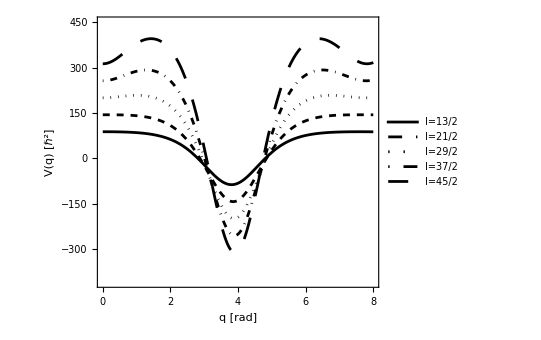

```mathematica
p1=Plot[{V[q,13/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,21/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,29/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,37/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,45/2,jConst,thetaConst,A1Const,A2Const,A3Const]},{q,0,8},AspectRatio->0.85,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"q [rad]","V(q) [ℏ^2]"},LabelStyle->{fontsize,Black,FontFamily->"Arial"},ImageMargins->0,PlotRangeClipping->False,ImageSize->imgsize,PlotStyle->{{Black,Thick},{Black,Dashed},{Black,Dotted},{Black,DotDashed},{Black,Dashing[0.04]}},PlotLegends->LineLegend[{"I=13/2","I=21/2","I=29/2","I=37/2","I=45/2"}],PlotRange->{-410,450}];
Show[p1]
export[p1,"Elliptic-Potential-V","eps"];
export[p1,"Elliptic-Potential-V","pdf"];
```

## Determine the period for the current parameters

```mathematica
kConsttheta=kterm[45/2,jConst,thetaConst,A1Const,A2Const,A3Const];
kConstthetapi=kterm[45/2,jConst,thetaConst+180,A1Const,A2Const,A3Const];
periodK=period[kConsttheta];
periodKpi=period[kConstthetapi];
qrange=4*periodK;
qrangepi=4*periodKpi;
```

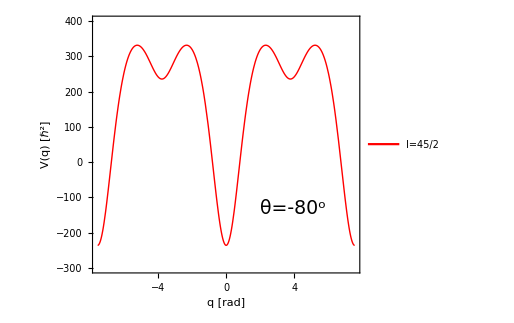

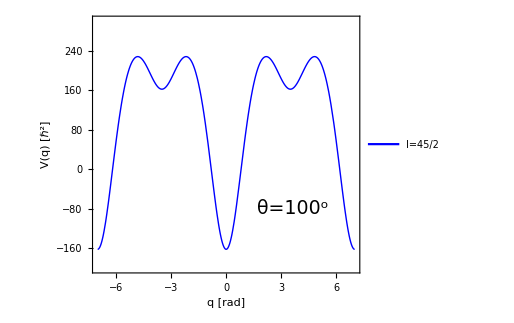

```mathematica
p2=Plot[{V[q,45/2,jConst,thetaConst,A1Const,A2Const,A3Const]},{q,-qrange,qrange},PlotRange->{Automatic,{-300,400}},AspectRatio->0.85,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"q [rad]","V(q) [ℏ^2]"},LabelStyle->{fontsize,Black,FontFamily->"Latin Modern Roman"},ImageMargins->0,PlotRangeClipping->False,ImageSize->imgsize,PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"I=45/2"},{0.25,0.25}],Epilog->{Inset[Style["θ=-80^o",19,Black,FontFamily->"Latin Modern Roman"],Scaled[{0.75,0.25}]]}];
Show[p2]
export[p2,"Elliptic-Potential-deep-1"];
p3=Plot[{V[q,45/2,jConst,thetaConst+180,A1Const,A2Const,A3Const]},{q,-qrangepi,qrangepi},PlotRange->{Automatic,{-200,300}},AspectRatio->0.85,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"q [rad]","V(q) [ℏ^2]"},LabelStyle->{fontsize,Black,FontFamily->"Latin Modern Roman"},ImageMargins->0,PlotRangeClipping->False,ImageSize->imgsize,PlotStyle->{{Blue,Thick}},PlotLegends->Placed[{"I=45/2"},{0.25,0.25}],Epilog->{Inset[Style["θ=100^o",19,Black,FontFamily->"Latin Modern Roman"],Scaled[{0.75,0.25}]]}];
Show[p3]
export[p3,"Elliptic-Potential-deep-1-180"];
```

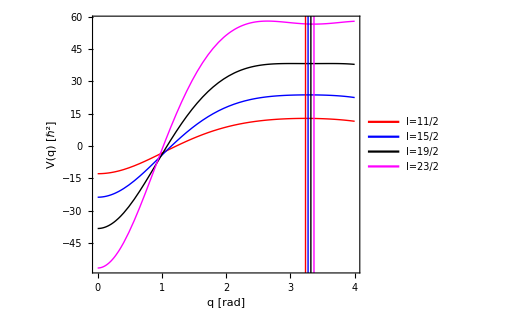

```mathematica
periodConst112=period[kterm[11/2,jConst,thetaConst,A1Const,A2Const,A3Const]];
periodConst152=period[kterm[15/2,jConst,thetaConst,A1Const,A2Const,A3Const]];
periodConst192=period[kterm[19/2,jConst,thetaConst,A1Const,A2Const,A3Const]];
periodConst232=period[kterm[23/2,jConst,thetaConst,A1Const,A2Const,A3Const]];
p4=Plot[{V[q,11/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,15/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,19/2,jConst,thetaConst,A1Const,A2Const,A3Const],V[q,23/2,jConst,thetaConst,A1Const,A2Const,A3Const]},{q,0,4},AspectRatio->0.85,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"q [rad]","V(q) [ℏ^2]"},LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},ImageMargins->0,PlotRangeClipping->False,ImageSize->imgsize,PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Magenta,Thick}},PlotLegends->Placed[{"I=11/2","I=15/2","I=19/2","I=23/2"},{0.75,0.25}]];
lines={Graphics[{Red,Line[{{2*periodConst112,-63.5},{2*periodConst112,64}}]}],Graphics[{Blue,Line[{{2*periodConst152,-63.5},{2*periodConst152,64}}]}],Graphics[{Black,Line[{{2*periodConst192,-63.5},{2*periodConst192,64}}]}],Graphics[{Magenta,Line[{{2*periodConst232,-63.5},{2*periodConst232,64}}]}]};
Show[p4,lines]
export[p4,"Elliptic-Potential-2K-Minima"];
```